```mathematica
Clear["Global`*"]
SetDirectory["/Users/brycemorsky/Desktop/New projects/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},PlotTheme->"Vibrant",BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
RD[i,p]
Solve[(1-p) p (-c-(i β)/2+i β-(1-p)^2 θ+p^2 θ)==0,p]
FullSimplify[D[(1-p) p (-c-(i β)/2+i β-(1-p)^2 θ+p^2 θ),p]/.{{p->0},{p->1},{p->(2 c-i β+2 θ)/(4 θ)}}]
```

RD[i,p]

{{p→0},{p→1},{p→(2 c-i β+2 θ)/(4 θ)}}

{-c+(i β)/2-θ,c-(i β)/2-θ,-(-2 c+i β)^2/(8 θ)+θ/2}

```mathematica
D[u[i,p,q],p]/.{q->p}
Simplify[u[i,1,p]-u[i,0,p]]
Solve[-c+(i p^(-1+η) β η)/((1+p^η)^2)==0,p]
```

-c+i β η

-c+i β η+(-1+2 p) θ

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-c+(i p^(-1+η) β η)/((1+p^η)^2)==0,p]

```mathematica
D[(1-p) p (-c-(i β)/2+i β-(1-p)^2 θ+p^2 θ),p]/.{{p->0},{p->1},{p->(2 c-i β+2 θ)/(4 θ)}}
```

(1-p) p (-c-(i β)/2+(i β)/(1+0^η)-(1-p)^2 θ+p^2 θ)

{{p→0},{p→1},{p→(2 c-i β+2 θ)/(4 θ)}}

```mathematica
(1-p) p (-c-(i β)/2+i β-(1-p)^2 θ+p^2 θ)
```

{{p→0},{p→1},{p→(2 c+2 0^η c-i β+0^η i β+2 θ+2 0^η θ)/(4 (1+0^η) θ)}}

```mathematica
g[p_]=1/(1+p^η);
g[p_]=1-η*p;
u[i_,p_,q_] = -β*g[p]*i-c*p-θ*(p-q)^2;
BRD[i_,p_]=1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])-p;
RD[i_,p_]=p*(1-p)*(u[i,1,p]-u[i,0,p]);
(* A couple different utility differences (between obeying or disobeying the norm. *)
SEIR={s'[t]==-β*g[p[t]]*s[t]*i[t],e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
SEIRS={s'[t]==-β*g[p[t]]*s[t]*i[t]+α*(1-s[t]-e[t]-i[t]),e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
```

```mathematica
rdeq=Solve[RD[i,p]==0,p]
```

{{p→0},{p→1},{p→(c-i β η+θ)/(2 θ)}}

```mathematica
FullSimplify[D[RD[i,p],p]/.rdeq]
```

{-c+i β η-θ,c-i β η-θ,(-(c-i β η)^2+θ^2)/(2 θ)}

```mathematica
eqs=FullSimplify[Solve[{-β*g[p]*s*i+α*(1-s-e-i)==0,β*g[p]*s*i-δ*e==0,δ*e-γ*i==0,ϵ*RD[i,p]==0},{s,e,i,p}]]
D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.eqs
```

```mathematica
s->γ/β,e->(α (β-γ) γ)/(β γ δ+α β (γ+δ)),i->(α (β-γ) δ)/(β γ δ+α β (γ+δ)),p->0
```

```mathematica
1/(β/γ)
```

0.243902

```mathematica
{a4,a3,a2,a1,a0}=FullSimplify[CoefficientList[CharacteristicPolynomial[D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.{s->γ/β,e->(α (β-γ) γ)/(β γ δ+α β (γ+δ)),i->(α (β-γ) δ)/(β γ δ+α β (γ+δ)),p->0},λ],λ]]
```

```mathematica
FullSimplify[a1*a2-a0*a3]
```

```mathematica
FullSimplify[-4. (0.+c-0.026956521739130428 η+θ)/.{η->0.8}]
```

-4. (-0.0215652+c+θ)

```mathematica
Eigenvalues[D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.{s->1,e->0,i->0,p->(c+θ)/(2 θ)}]
```

```mathematica
FullSimplify[-γ-δ+√(γ^2+4 (γ+n) δ-2 γ δ+δ^2-4 (γ+n) δ η)]
```

-γ-δ+√(4 n δ+(γ+δ)^2-4 (n+γ) δ η)

```mathematica
FullSimplify[-2 c β δ η θ^7+γ^2 θ^8+4 β δ θ^8-2 γ δ θ^8+δ^2 θ^8-2 β δ η θ^8-(γ*θ^4+δ*θ^4)^2]
```

-2 δ θ^7 (c β η+2 γ θ+β (-2+η) θ)

```mathematica
Simplify[c 2 η+2 θ+2(-2+η) θ]
```

2 (c η+(-1+η) θ)

```mathematica
(* Parameters *)
α=0.01;
β=0.41;
γ=0.1;
δ=0.2;
ϵ=1;
κ=100;
(*c=0.025;*)
(*η=0.8;*)
```

-Graphics3D-

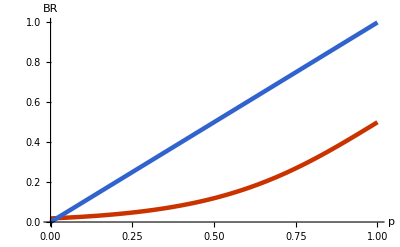

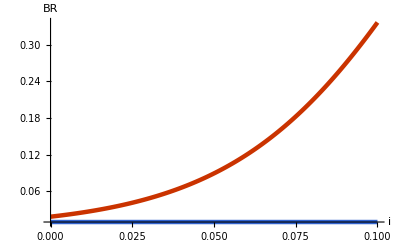

-Graphics3D-

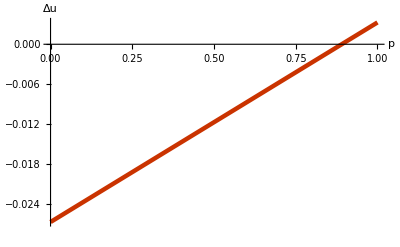

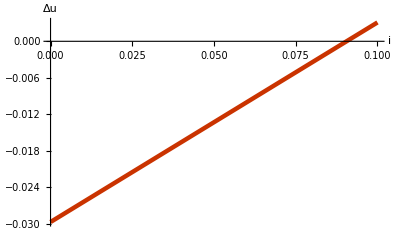

```mathematica
Plot3D[Evaluate[{1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])]),p}/.{c->0.03,η->0.8}],{p,0,1},{i,0,0.1},PlotRange->{{0,1},{0,0.1}},PlotPoints->100,AxesLabel->{"p","i","BR"}]
Plot[Evaluate[{1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])]),p}/.{i->0.0,c->0.02,η->0.8}],{p,0,1},PlotPoints->100,AxesLabel->{"p","BR"},PlotRange->Full]
Plot[Evaluate[{1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])]),p}/.{p->0.01,c->0.02,η->0.8}],{i,0,0.1},PlotPoints->100,AxesLabel->{"i","BR"},PlotRange->Full]
Plot3D[Evaluate[u[i,1,p]-u[i,0,p]/.{c->0.015,η->0.8}],{p,0,1},{i,0,0.1},PlotRange->{{0,1},{0,0.1}},PlotPoints->100,AxesLabel->{"p","i","Δu"}]
Plot[Evaluate[u[i,1,p]-u[i,0,p]/.{i->0.01,c->0.015,η->0.8}],{p,0,1},PlotPoints->100,AxesLabel->{"p","Δu"}]
Plot[Evaluate[u[i,1,p]-u[i,0,p]/.{p->0.01,c->0.015,η->0.8}],{i,0,0.1},PlotPoints->100,AxesLabel->{"i","Δu"},PlotRange->Full]
```

```mathematica
RD[0.05,p[t]]/.{c->0.001,η->0.79,θ->0.001}
```

(1-p[t]) p[t] (0.015195-0.001 (1-p[t])^2+0.001 p[t]^2)

```mathematica
Solve[{0.00656-1. c+(-1.+2. p) θ==0,0.0328-2 c==0},{c,θ}]
```

{{c→0.0164}}

```mathematica
Export["plt333.png",plt3,ImageResolution->200];
```

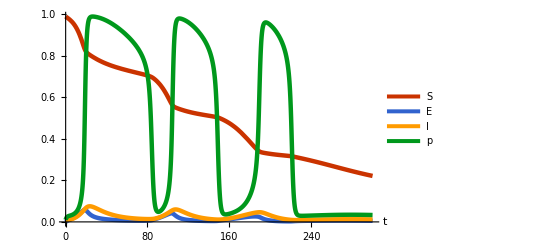

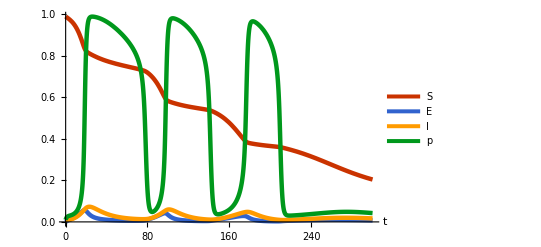

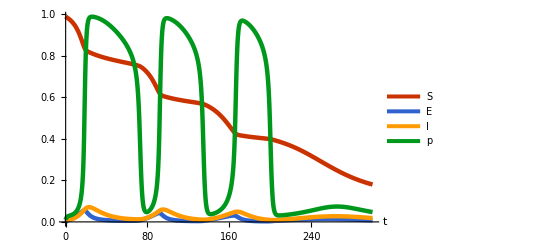

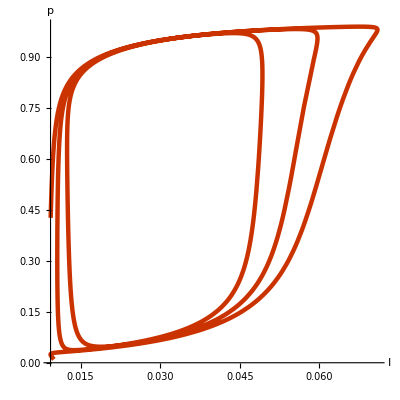

```mathematica
θ=0.03;
sol=NDSolve[Join[SEIR/.{c->0.01,η->0.88},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,η->0.9},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,η->0.92},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
plt4=ParametricPlot[Evaluate[{i[t],p[t]}/.sol],{t,0,200},PlotRange->Full,AspectRatio->1,AxesLabel->{"I","p"}]
(*Export["plt1.png",plt1,ImageResolution->200];
Export["plt2.png",plt2,ImageResolution->200];
Export["plt3.png",plt3,ImageResolution->200];
Export["plt4.png",plt4,ImageResolution->200];*)
```

```mathematica
Export["plt4444.png",plt4,ImageResolution->200];
```

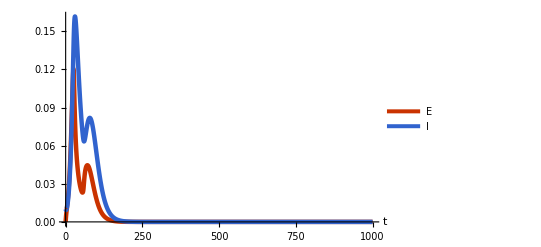

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
```

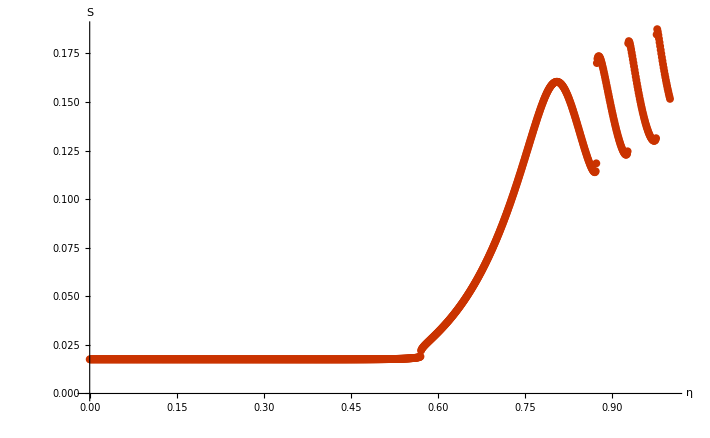

```mathematica
sfin=Array[n,{1001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->0.01,η->2*j/1000-1},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt5=ListPlot[sfin,PlotStyle->PointSize[0.008],AxesLabel->{"η","S"}]
(*Export["plt5BR.png",plt5,ImageResolution->200];*)
```

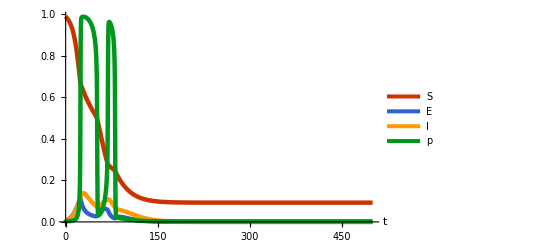

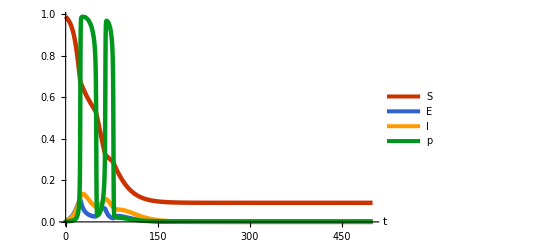

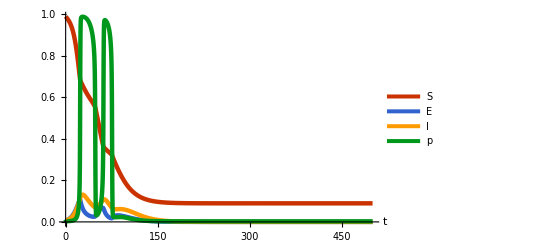

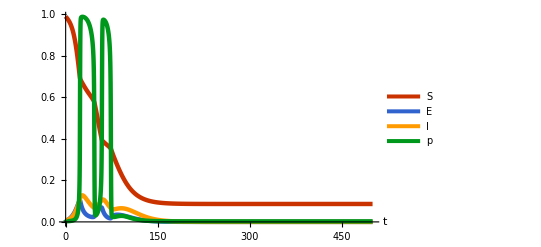

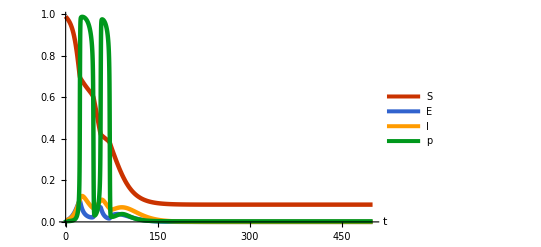

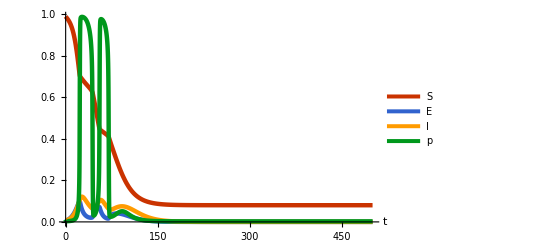

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.8},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.82},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.84},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.86},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.88},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.03,η->0.9},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```

```mathematica
c=0.02;
sfin=Array[n,{1001*51,3}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{θ->k/1000,η->j/1000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},{0.001*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000},{k,0,50}];
plt7 = ListPlot3D[sfin,AxesLabel->{"θ","c","S"}]
(*Export["plt7RD.png",plt7,ImageResolution->200]*);
```

-Graphics3D-

```mathematica
plt7 = ListPlot3D[sfin,AxesLabel->None]
Export["plt7theta.png",plt7,ImageResolution->200];
```

-Graphics3D-

```mathematica
Show[plt7,Axes->False]
```

-Graphics3D-

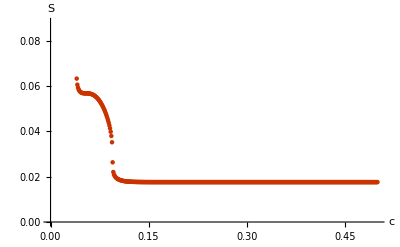

```mathematica
vtheta=Array[n,{501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->k/1000,η->0.95},ics],{s,e,i,p},{t,0,1000}];
vtheta[[count]]= Join[{0.001*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{k,0,500}];
plt6=ListPlot[vtheta,PlotStyle->PointSize[0.008],AxesLabel->{"c","S"}]
(*Export["plt6.png",plt6,ImageResolution->200]*);
```

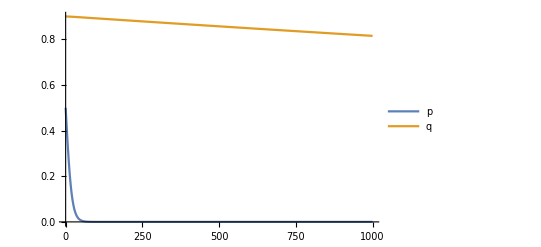

```mathematica
b=2;
c=1;
α=0.9;
ϵ=0.0001;
eqn={p'[t]==p[t]*(1-p[t])*(p[t]*(b-c+α*(1-q[t]))+(1-p[t])*(-c+α*(1-q[t]))-p[t]*(b-α*q[t])-(1-p[t])*(-α*q[t])),q'[t]==ϵ*(p[t]-q[t])};
ic={p[0]==0.5,q[0]== 0.9};
sols=NDSolve[Join[eqn,ic],{p,q},{t,0,1000}];
Plot[Evaluate[{p[t],q[t]}/.sols],{t,0,1000},PlotRange->All,PlotLegends->{"p","q"},AxesLabel->{"t"}]
```

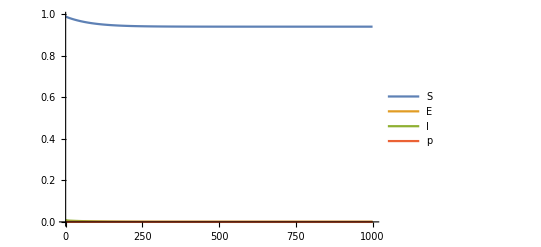

```mathematica
sol=NDSolve[Join[{s'[t]==-β*(1-m)*s[t]*i[t],e'[t]==β*(1-m)*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*(1/(1+Exp[-100*(p[t]+θ*i[t]-1)])-p[t])}/.{m->0.79,c->20},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```